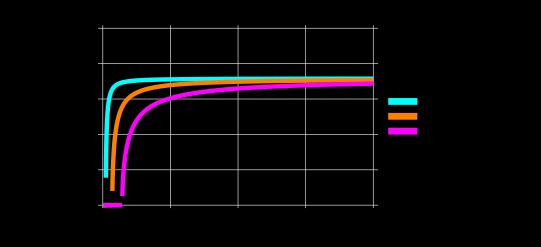

```mathematica
(*Grover Protocol:Multi-Scale Batch Audit (Dwarf,Spiral,Elliptical)*)ClearAll["Global`*"];

(*Global R-invariant*)
R=1.15428;

(*Grover Velocity Function*)
vGrover[r_,s_]:=Sqrt[Max[0,r*(-2*s/r^3+R/(r+s))]];

(*Galaxy Parameters:{Name,ScaleParameter s,PlotColor}*)
galaxyBatch={{"Dwarf (High Memory Lag)",0.2,Cyan},{"Spiral (Standard Audit)",1.5,Orange},{"Elliptical (Massive Buffer)",5.0,Magenta}};

(*---Batch Visualization---*)
batchPlot=Plot[Evaluate[Table[vGrover[r,g[[2]]],{g,galaxyBatch}]],{r,0.1,60},PlotRange->{0,1.5},PlotStyle->Table[{g[[3]],Thickness[0.008]},{g,galaxyBatch}],Frame->True,FrameLabel->{"Radius (kpc)","Circular Velocity (Normalized)"},PlotLabel->Style["Grover Batch Audit: Universality of R = 1.15428",14],PlotLegends->SwatchLegend[galaxyBatch[[All,3]],galaxyBatch[[All,1]]],Background->Black,FrameStyle->White,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]];

Print[batchPlot];
```